```mathematica
numeraiData=Import["/home/tamellan/Desktop/Numerai/numerai_training_data.csv"];
numeraiData//Dimensions
```

{535714,54}

```mathematica
results={}; 
(*For[factor=10;i=1,i<2,i++,trainSetSize=i*factor;*)
For[q=1,q<6,q++,Print[q];

(*Training set size parameters*)
trainSetSize=q^3*200;
testSetSize=q^3*100;


correlationTable=Table[{k,Correlation[Table[Transpose[numeraiData[[-trainSetSize;;-1]]][[i]][[2;;-1]],{i,k,k}][[1]],Table[Transpose[numeraiData[[-trainSetSize;;-1]]][[i]][[2;;-1]],{i,54,54}][[1]]]},{k,4,54}];
bestCorrelations=Reverse@Ordering[Abs@Transpose[correlationTable][[2]]][[-10;;-1]];
"Correlations";
correlationTable[[bestCorrelations]];
bestCorrs=Transpose[correlationTable[[bestCorrelations]]][[1]];
topfeatures=bestCorrs;
(*Select traingin and esting sets*)
topTen=Transpose[numeraiData[[-trainSetSize;;-1]]][[bestCorrs]];
(*topTenVal=Transpose[numeraiData[[-500;;-400]]][[bestCorrs]];*)
topTenTest=Transpose[numeraiData[[-(testSetSize+trainSetSize);;-trainSetSize]]][[bestCorrs]];

(*Training*)
trainInput=Transpose[topTen[[2;;-1]]];
trainOutput=topTen[[1]];
(*Validation
trainInputVal=Transpose[topTenVal[[2;;-1]]];
trainOutputVal=topTenVal[[1]];*)
(*Test*)
trainInputTest=Transpose[topTenTest[[2;;-1]]];
trainOutputTest=topTenTest[[1]];

(*Map input to output*)
f[arg_]:=arg[[1]]->arg[[2]];
trainSet=Table[f[{trainInput[[i]],trainOutput[[i]]}],{i,1,Length[trainInput]}];
trainSetTest=Table[f[{trainInputTest[[i]],trainOutputTest[[i]]}],{i,1,Length[trainInputTest]}];

(*methods={"LinearRegression","GaussianProcess","NearestNeighbors","NeuralNetwork","RandomForest"};*)
methods={"LinearRegression"};

(*Train Net*)
nets=Table[Predict[trainSet,Method->methods[[i]],PerformanceGoal->"Quality"],{i,1,Length@methods}]//AbsoluteTiming;
timings=StringJoin[{"Timing to train net is: ",ToString@nets[[1]]," seconds"}];
net=nets[[2]];

(*Apply net to the training data*)
netTrainOutput=Table[Table[net[[j]][trainInput[[i]]],{i,1,Length@trainInput}],{j,1,Length@net}];

actualTrain=Table[{i,trainOutput[[i]]},{i,1,Length[trainInput]}];
netTrain=Table[Table[{i,netTrainOutput[[j]][[i]]},{i,1,Length[trainInput]}],{j,1,Length@net}];

(*Apply net to the testing data*)

netTrainOutputTest=Table[Table[net[[j]][trainInputTest[[i]]],{i,1,Length@trainInputTest}],{j,1,Length@net}];

actualTrainTest=Table[{i,trainOutputTest[[i]]},{i,1,Length[trainInputTest]}];
netTrainTest=Table[Table[{i,netTrainOutputTest[[j]][[i]]},{i,1,Length[trainInputTest]}],{j,1,Length@net}];

(*Analyse results*)
(*Predicted and actual results on test data*)
trueResults=Transpose[actualTrainTest][[2]];
predictedResults=Transpose[netTrainTest[[1]]][[2]];


(*Define log loss function*)
Clear[logloss];
loglossfun[binary_,prediction_]:=Table[-(binary[[i]]*Log[prediction[[i]]]+(1-binary[[i]])*Log[1-prediction[[i]]]),{i,1,Length@binary}];
(*Calculate the log loss for each time step, then find the mean*)
"The log loss is: ";
logloss=Mean@loglossfun[trueResults,predictedResults];

loglossRollingFun[binary_,prediction_]:=Table[Table[-(binary[[i]]*Log[prediction[[i]]]+(1-binary[[i]])*Log[1-prediction[[i]]]),{i,1,j}],{j,1,Length@binary}];
rollingLogLoss=Mean/@loglossRollingFun[trueResults,predictedResults];
rollingLogLossSD=StandardDeviation/@loglossRollingFun[trueResults,predictedResults][[2;;-1]];

"The log loss SD is: ";
rollingLogLossSD[[-1]];

"The log loss accuracy is: ";
rollingLogLossSD[[-1]]/Sqrt[testSetSize];

(*Define binary accuracy*)
polar2[f_]:=Table[If[f[[i]]>Mean[f],1,0],{i,1,Length@f}];
polarisedOutputTest2=Table[polar2@netTrainOutputTest[[i]],{i,1,Length[net]}];
(*Output binary accuracy - method, correlation, success*)
jobsize=Table[{"Training set size is: ",trainSetSize," and testing set size is: ",testSetSize},1]//TableForm;
"Method, correlation, success %, log loss, log loss accuracy";
scores=Table[{methods[[i]],Correlation[trainOutputTest,polarisedOutputTest2[[i]]],(Correlation[trainOutputTest,polarisedOutputTest2[[i]]]+1)/2//N,logloss,rollingLogLossSD[[-1]]/Sqrt[testSetSize]},{i,1,Length@methods}]//N//TableForm;
index=q;
jobScores={q,jobsize,timings,Join["Best features: ",ToString@topfeatures],scores}//TableForm;
AppendTo[results,jobScores]]
numeraiTest=results//TableForm;
Export["/home/tamellan/Desktop/Numerai/numeraiTest.dat",results]
numeraiTest
```

1

2

3

4

/home/tamellan/Desktop/Numerai/numeraiTest.dat

1
Training set size is:  | 200 |  and testing set size is:  | 100
Timing to train net is: 0.066914 seconds
Join[Best features: ,{54, 11, 33, 47, 17, 52, 19, 44, 35, 39}]
LinearRegression | 0.0282797 | 0.51414 | 0.742979-0.0311049 ⅈ | 0.0531955
2
Training set size is:  | 400 |  and testing set size is:  | 200
Timing to train net is: 0.05829 seconds
Join[Best features: ,{54, 11, 20, 35, 33, 44, 52, 37, 19, 47}]
LinearRegression | 0.0238309 | 0.511915 | 0.697219 | 0.00930553
3
Training set size is:  | 600 |  and testing set size is:  | 300
Timing to train net is: 0.079726 seconds
Join[Best features: ,{54, 11, 35, 37, 33, 47, 52, 9, 20, 40}]
LinearRegression | -0.0166453 | 0.491677 | 0.695296 | 0.00603806
4
Training set size is:  | 800 |  and testing set size is:  | 400
Timing to train net is: 0.06261 seconds
Join[Best features: ,{54, 9, 35, 18, 37, 11, 45, 17, 43, 34}]
LinearRegression | 0.0448286 | 0.522414 | 0.695364 | 0.00579924

```mathematica
(*Visualisations*)
p1=ListLinePlot[{rollingLogLoss,Table[logloss,Length@rollingLogLoss]},PlotRange->{Automatic,{0.683,0.72}},PlotLegends->{"Logloss convergence","Logloss"},FrameLabel->{"datapoint","logloss"},Frame->True,ImageSize->500];
p2=ListLinePlot[Table[rollingLogLossSD[[i]]/Sqrt[i],{i,1,Length@rollingLogLossSD-1}],PlotLegends->{"sd/Sqrt[i]"},FrameLabel->{"datapoint","accuracy"},Frame->True,ImageSize->500];
GraphicsGrid[{{p1,p2}},ImageSize->{1300,740},Spacings->0]
```

-Graphics-

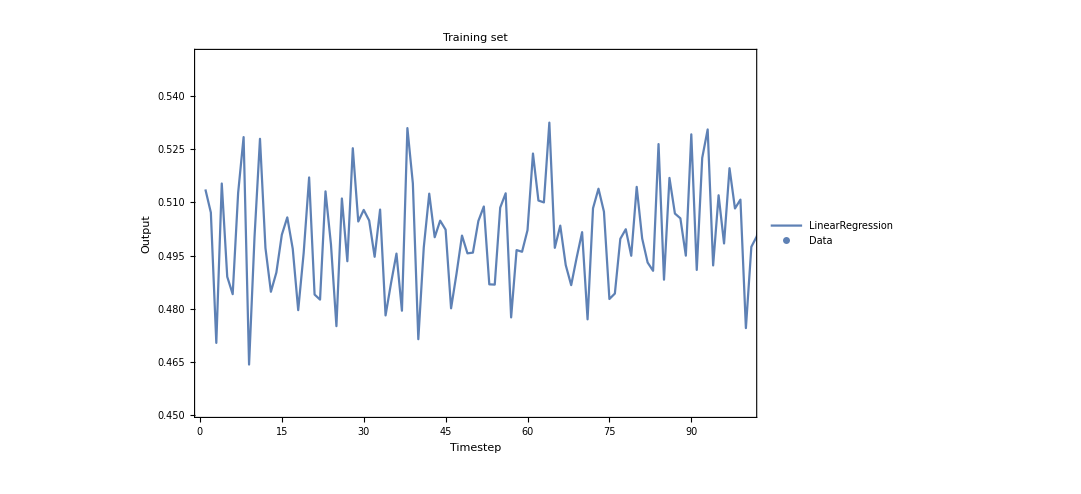

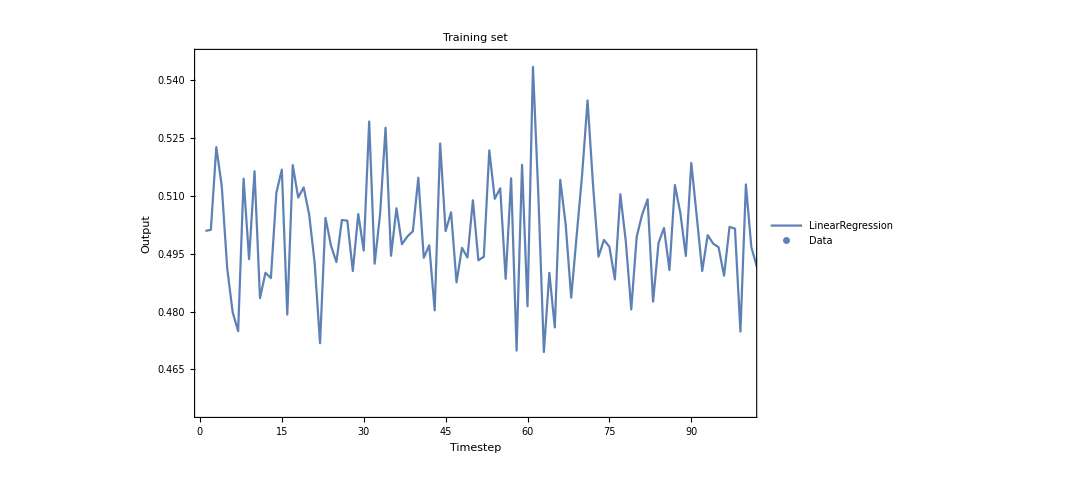

```mathematica
style[arg_]:=Table[Style[arg[[i]],16,Black],{i,1,Length@arg}]
plotOpts={PlotLegends->Placed[style[methods],{0.15,0.28}],Frame->True,FrameLabel->{Style["Timestep",18,Black],Style["Output",18,Black]},FrameStyle->Directive[Thickness[0.004],Black],ImageSize->800,FrameTicksStyle->18,PlotRange->{{1,100},Automatic}};Show[{ListLinePlot[netTrain,Evaluate@plotOpts,PlotLabel->Style["Training set",Black,18]],ListPlot[actualTrain,PlotLegends->Placed[{Style["Data",16,Black]},{0.45,0.85}]]}]
Show[{ListLinePlot[netTrainTest,Evaluate@plotOpts,PlotLabel->Style["Training set",Black,18]],ListPlot[actualTrainTest,PlotLegends->Placed[{Style["Data",16,Black]},{0.45,0.85}]]}]
```

```mathematica
(*2000training, 2000testing - {{"LinearRegression", 0.1005278214652477, 0.5502639107326238, 0.6867619038430586, 0.001888464122952996}}*)

(*"<Training set size is: > | 20000 | < and testing set size is: > | 2000"
"0.100528 | 0.550264 | 0.686762 | 0.00188846"*)

(*"<Training set size is: > | 20000 | < and testing set size is: > | 2000"
"<LinearRegression> | 0.0395861 | 0.519793 | 0.691382 | 0.000659451"*)

(*{{"Training set size is: ", 50000, " and testing set size is: ", 2000}}
{{"LinearRegression", 0.06279176276996125, 0.5313958813849806, 0.6914105407186204, 0.000617750029293622}}*)

(*
{{"Training set size is: ", 100000, " and testing set size is: ", 2000}}
{{"LinearRegression", 0.06058740727249449, 0.5302937036362473, 0.6914962253481756, 0.0012635619913129708}}
*)

(*
{{"Training set size is: ", 100000, " and testing set size is: ", 10000}}
{{"LinearRegression", 0.017685491864945474, 0.5088427459324727, 0.6931632842153858, 0.000558918026093522}}
*)
```